```mathematica
SetDirectory[NotebookDirectory[]];
U=(3/2 -x[t] -1)^ 2 + (1/2)(2x[t] -1)^ 2 + (1/2) Subscript[Γ, 1](2x[t] )^ 2+Subscript[Γ, 2](3/2 -x[t] )^2 + Subscript[T, 1] 2x[t] + 2 Subscript[T, 2](3/2 -x[t]);
```

```mathematica
dxdt =FullSimplify[ -D[U,x[t] ]];
```

## General solution x(t):

```mathematica
Subscript[x, gen]= FullSimplify[DSolve[x'[t]==dxdt, x[t],t]][[1,1,2]];
```

## General solution L01(t):

```mathematica
dL01dt =  -Subscript[K, L](Subscript[L0, 1][t]-2 Subscript[x, gen]);
```

```mathematica
Subscript[L01, gen]=FullSimplify[Expand[ FullSimplify[DSolve[Subscript[L0, 1]'[t]==dL01dt, Subscript[L0, 1][t],t]][[1,1,2]] ]];
```

## General solution L02 (t) :

```mathematica
dL02dt =  -Subscript[K, L](Subscript[L0, 2][t]-(3/2 -Subscript[x, gen]));
```

```mathematica
Subscript[L02, gen]=FullSimplify[Expand[ FullSimplify[DSolve[Subscript[L0, 2]'[t]==dL02dt, Subscript[L0, 2][t],t]][[1,1,2]] ]];
```

## Summary general solutions :

```mathematica
Subscript[x, gen]//TraditionalForm
```

(3 Γ_2-2 T_1+2 T_2+3)/(4 Γ_1+2 Γ_2+6)+1 ⅇ^(-2 (2 Γ_1+Γ_2+3) t)

```mathematica
Subscript[L01, gen]//TraditionalForm
```

3/(2 Γ_1+Γ_2+3)+(2 1 K_L ⅇ^(-2 (2 Γ_1+Γ_2+3) t))/(K_L-2 (2 Γ_1+Γ_2+3))+2 ⅇ^(-t K_L)+(3 Γ_2-2 T_1+2 T_2)/(2 Γ_1+Γ_2+3)

```mathematica
Subscript[L02, gen]//TraditionalForm
```

3/(2 Γ_1+Γ_2+3)+(1 K_L ⅇ^(-2 (2 Γ_1+Γ_2+3) t))/(4 Γ_1+2 Γ_2-K_L+6)+2 ⅇ^(-t K_L)+(3 Γ_1+T_1-T_2)/(2 Γ_1+Γ_2+3)

```mathematica
x00 = (3 Subscript[Γ, 2]-2 Subscript[T, 1]+2 Subscript[T, 2]+3)/(4 Subscript[Γ, 1]+2 Subscript[Γ, 2]+6)//Simplify
```

(3-2 T_1+2 T_2+3 Γ_2)/(6+4 Γ_1+2 Γ_2)

```mathematica
L001 = 3/(2 Subscript[Γ, 1]+Subscript[Γ, 2]+3)+(3 Subscript[Γ, 2]-2 Subscript[T, 1]+2 Subscript[T, 2])/(2 Subscript[Γ, 1]+Subscript[Γ, 2]+3)//Simplify
```

(3-2 T_1+2 T_2+3 Γ_2)/(3+2 Γ_1+Γ_2)

```mathematica
L002 = 3/(2 Subscript[Γ, 1]+Subscript[Γ, 2]+3)+(3 Subscript[Γ, 1]+Subscript[T, 1]-Subscript[T, 2])/(2 Subscript[Γ, 1]+Subscript[Γ, 2]+3)//Simplify
```

(3+T_1-T_2+3 Γ_1)/(3+2 Γ_1+Γ_2)

## Phase 1 : t_abs=0, x(t=0)=x00, Γ_1=α, Γ_2=0, L0_1=L001,L0_2=L002]

```mathematica
Subscript[c1, p1]= Solve[{Subscript[x, gen]/.{t->0,Subscript[Γ, 1]->α}/.{Subscript[Γ, 2]->0}}=={x00/.{Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->0}},C[1]][[1,1,2]];
```

```mathematica
Subscript[c2, p1]= Solve[{Subscript[L01, gen]/.{t->0,Subscript[Γ, 1]->α}/.{Subscript[Γ, 2]->0}/.{C[1]->Subscript[c1, p1]}}=={L001/.{Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->0}},C[2]][[1,1,2]];
```

```mathematica
Subscript[c3, p1]= Solve[{Subscript[L02, gen]/.{t->0,Subscript[Γ, 1]->α}/.{Subscript[Γ, 2]->0}/.{C[1]->Subscript[c1, p1]}}=={L002/.{Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->0}},C[2]][[1,1,2]];
```

```mathematica
Subscript[x, p1]=Subscript[x, gen]/.{C[1]->Subscript[c1, p1],Subscript[Γ, 1]->α, Subscript[Γ, 2]->0};
```

```mathematica
Subscript[L01, p1]=Subscript[L01, gen]/.{C[1]->Subscript[c1, p1],C[2]->Subscript[c2, p1],Subscript[Γ, 1]->α, Subscript[Γ, 2]->0};
```

```mathematica
Subscript[L02, p1]=Subscript[L02, gen]/.{C[1]->Subscript[c1, p1],C[2]->Subscript[c3, p1],Subscript[Γ, 1]->α, Subscript[Γ, 2]->0};
```

### Γ_2 gets activated when ϵ_2(t^*)>=ϵ_c. Let’s write an equation for t^*:

```mathematica
Subscript[l2, p1]=3/2-Subscript[x, p1];
```

```mathematica
ff =(Subscript[l2, p1]-Subscript[L02, p1]) -Subscript[L02, p1] Subscript[ϵ, c];
```

#### The above Eq ff==0 defines the condition over (K_L,τ) such that the activity can propagate from unit 1 to the lateral units in this Phase1 (i.e., t_abs<τ). This equation can not be analytically solved.

## Phase 2 (starting at t_abs=t^*=ta_1) : t=0,x(t=0)=x_p1(t=ta_1), Γ_1=α, Γ_2=α, L0_1=L01_p1(t=ta_1),L0_2=L02_p1(t=ta_1)]

```mathematica
Subscript[c1, p2]= Solve[{Subscript[x, gen]/.{t->0,Subscript[Γ, 1]->α}/.{Subscript[Γ, 2]->α}}=={Subscript[x, p1]/.{t->Subscript[ta, 1]}},C[1]][[1,1,2]];
```

```mathematica
Subscript[c2, p2]=Solve[{Subscript[L01, gen]/.{t->0,Subscript[Γ, 1]->α}/.{Subscript[Γ, 2]->α}/.{C[1]->Subscript[c1, p2]}}=={Subscript[L01, p1]/.{t->Subscript[ta, 1]}},C[2]][[1,1,2]];
```

```mathematica
Subscript[x, p2]=Subscript[x, gen]/.{C[1]->Subscript[c1, p2],Subscript[Γ, 1]->α, Subscript[Γ, 2]->α};
```

```mathematica
Subscript[L01, p2]=Subscript[L01, gen]/.{C[1]->Subscript[c1, p2],C[2]->Subscript[c2, p2],Subscript[Γ, 1]->α, Subscript[Γ, 2]->α};
```

## Phase 3 (starting at time t_abs=τ, x(t=0)=x_p2(τ-ta_1),Γ_1->0,Γ_2->α, L0_1=L01_p2(τ-ta_1))

```mathematica
Subscript[c1, p3]=Solve[{Subscript[x, gen]/.{t->0,Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->α}}=={Subscript[x, p2]/.{t->τ-Subscript[ta, 1]}},C[1]][[1,1,2]];
```

```mathematica
Subscript[c2, p3]= Solve[{Subscript[L01, gen]/.{t->0,Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->α}/.{C[1]->Subscript[c1, p3]}}=={Subscript[L01, p2]/.{t->τ-Subscript[ta, 1]}},C[2]][[1,1,2]];
```

```mathematica
Subscript[x, p3]=Subscript[x, gen]/.{C[1]->Subscript[c1, p3],Subscript[Γ, 1]->0, Subscript[Γ, 2]->α};
```

```mathematica
Subscript[L01, p3]=Subscript[L01, gen]/.{C[1]->Subscript[c1, p3],C[2]->Subscript[c2, p3],Subscript[Γ, 1]->0, Subscript[Γ, 2]->α};
```

## Phase 4 (starting at time t_abs=τ+ta_1, x(t=0)=x_p3(ta_1),Γ_1->0,Γ_2->0, L0_1=L01_p2(ta_1))

```mathematica
Subscript[c1, p4]= Solve[{Subscript[x, gen]/.{t->0,Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->0}}=={Subscript[x, p3]/.{t->Subscript[ta, 1]}},C[1]][[1,1,2]];
```

```mathematica
Subscript[c2, p4]= Solve[{Subscript[L01, gen]/.{t->0,Subscript[Γ, 1]->0}/.{Subscript[Γ, 2]->0}/.{C[1]->Subscript[c1, p4]}}=={Subscript[L01, p3]/.{t->Subscript[ta, 1]}},C[2]][[1,1,2]];
```

```mathematica
Subscript[x, p4]=Subscript[x, gen]/.{C[1]->Subscript[c1, p4],Subscript[Γ, 1]->0, Subscript[Γ, 2]->0};
```

```mathematica
Subscript[L01, p4]=Subscript[L01, gen]/.{C[1]->Subscript[c1, p4],C[2]->Subscript[c2, p4],Subscript[Γ, 1]->0, Subscript[Γ, 2]->0};
```

## Finally, the condition for reactivation (at the minimum time t_abs=2τ) of the unit 1 is given by ϵ_(1p4)(t=τ-ta_1)>=ϵ_c:

```mathematica
Subscript[l1, p4]=2 Subscript[x, p4];
```

```mathematica
qq =Subscript[l1, p4]-Subscript[L01, p4](1+Subscript[ϵ, c])/.{t->τ-Subscript[ta, 1] };
```

## Now we numerically solve the boundaries for initial activity propagation (Eq ff), and for unit 1 reactivation (Eq qq):

#### We do a change of variable: y =ⅇ^-t

```mathematica
<<MaTeX`
```

```mathematica
Collect[Expand[ff],{ⅇ^(-2 t (3+2 α)), ⅇ^(-t Subscript[K, L]) }]
```

3/2-3/(3+2 α)-(3 α)/(3+2 α)-3/(6+4 α)-T_1/(3+2 α)+(2 T_1)/(6+4 α)+T_2/(3+2 α)-(2 T_2)/(6+4 α)-(3 ϵ_c)/(3+2 α)-(3 α ϵ_c)/(3+2 α)-(T_1 ϵ_c)/(3+2 α)+(T_2 ϵ_c)/(3+2 α)+ⅇ^(-t K_L) ((2 α)/(6+4 α-K_L)-(4 α T_1)/(3 (6+4 α-K_L))+(4 α T_2)/(3 (6+4 α-K_L))+(2 α ϵ_c)/(6+4 α-K_L)-(4 α T_1 ϵ_c)/(3 (6+4 α-K_L))+(4 α T_2 ϵ_c)/(3 (6+4 α-K_L)))+ⅇ^(-2 t (3+2 α)) (-α/(3+2 α)-(α K_L)/((3+2 α) (6+4 α-K_L))+(2 α T_1)/(3 (3+2 α))+(2 α K_L T_1)/(3 (3+2 α) (6+4 α-K_L))-(2 α T_2)/(3 (3+2 α))-(2 α K_L T_2)/(3 (3+2 α) (6+4 α-K_L))-(α K_L ϵ_c)/((3+2 α) (6+4 α-K_L))+(2 α K_L T_1 ϵ_c)/(3 (3+2 α) (6+4 α-K_L))-(2 α K_L T_2 ϵ_c)/(3 (3+2 α) (6+4 α-K_L)))

```mathematica
fftosolve=(3/2-3/(3+2 α)-(3 α)/(3+2 α)-3/(6+4 α)-Subscript[T, 1]/(3+2 α)+(2 Subscript[T, 1])/(6+4 α)+Subscript[T, 2]/(3+2 α)-(2 Subscript[T, 2])/(6+4 α)-(3 Subscript[ϵ, c])/(3+2 α)-(3 α Subscript[ϵ, c])/(3+2 α)-(Subscript[T, 1] Subscript[ϵ, c])/(3+2 α)+(Subscript[T, 2] Subscript[ϵ, c])/(3+2 α))+y^Subscript[K, L] ((2 α)/(6+4 α-Subscript[K, L])-(4 α Subscript[T, 1])/(3 (6+4 α-Subscript[K, L]))+(4 α Subscript[T, 2])/(3 (6+4 α-Subscript[K, L]))+(2 α Subscript[ϵ, c])/(6+4 α-Subscript[K, L])-(4 α Subscript[T, 1] Subscript[ϵ, c])/(3 (6+4 α-Subscript[K, L]))+(4 α Subscript[T, 2] Subscript[ϵ, c])/(3 (6+4 α-Subscript[K, L])))+y^(2  (3+2 α))(-α/(3+2 α)-(α Subscript[K, L])/((3+2 α) (6+4 α-Subscript[K, L]))+(2 α Subscript[T, 1])/(3 (3+2 α))+(2 α Subscript[K, L] Subscript[T, 1])/(3 (3+2 α) (6+4 α-Subscript[K, L]))-(2 α Subscript[T, 2])/(3 (3+2 α))-(2 α Subscript[K, L] Subscript[T, 2])/(3 (3+2 α) (6+4 α-Subscript[K, L]))-(α Subscript[K, L] Subscript[ϵ, c])/((3+2 α) (6+4 α-Subscript[K, L]))+(2 α Subscript[K, L] Subscript[T, 1] Subscript[ϵ, c])/(3 (3+2 α) (6+4 α-Subscript[K, L]))-(2 α Subscript[K, L] Subscript[T, 2] Subscript[ϵ, c])/(3 (3+2 α) (6+4 α-Subscript[K, L])));
```

```mathematica
Result for equal tensions:
```

```mathematica
t1s = {};KlsEff ={};
Kls =Flatten[{{0},Range[150] 0.05}];
alpha=1;Ec=0.1;
For[i=1,i<Length[Kls]+1, i++,
Kl=Kls[[i]];
soln=Solve[{fftosolve/.{α->alpha, Subscript[ϵ, c]->Ec}/.{Subscript[K, L]->Kl}/.{Subscript[T, 1]->0.1, Subscript[T, 2]->0.1}} == 0 &&y>0 &&y<1,y, Reals];
If[Length[soln]>0,
tau=- Log[soln[[Length[soln],1,2]]];
AppendTo[t1s,tau];AppendTo[KlsEff,Kl]]];
pares={};
For[i=1,i<Length[KlsEff]+1, i++,
Kl=Kls[[i]];t1=t1s[[i]];
ss=Solve[FullSimplify[{qq/.{α->alpha, Subscript[ϵ, c]->Ec}/.{Subscript[K, L]->Kl}/.{Subscript[ta, 1]->t1}/.{Subscript[T, 1]->0.1, Subscript[T, 2]->0.1}}]==0&&τ≥t1 ,τ, Reals];
tt=ss[[Length[ss],1,2]];
AppendTo[pares,tt]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

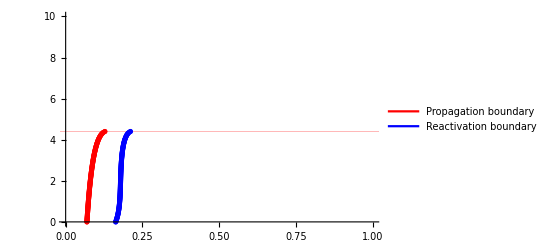

```mathematica
data=Transpose@{t1s,KlsEff};
data2=Transpose@{pares,KlsEff};
fig1=ListPlot[{data,data2},AxesLabel->{Style[MaTeX["\\tau[\\mu/k]",FontSize->30],Bold,16],Style[MaTeX["K_L[k/\\mu]",FontSize->30],Bold,16]},PlotRange->{{0,1},{0,10}}, PlotStyle->{Red,Blue},Joined->True,Mesh->Full,ImageSize->400,GridLines->{{},{{KlsEff[[Length[KlsEff]]],Red}}},PlotLegends->LineLegend[{"Propagation boundary","Reactivation boundary"},LegendMarkers->Automatic]]
```

```mathematica
Result for short middle-junction: T1=0.4, T2=0.1:
```

```mathematica
t1s = {};KlsEff ={};
Kls =Flatten[{{0},Range[150] 0.05}];
alpha=1;Ec=0.1;
For[i=1,i<Length[Kls]+1, i++,
Kl=Kls[[i]];
soln=Solve[{fftosolve/.{α->alpha, Subscript[ϵ, c]->Ec}/.{Subscript[K, L]->Kl}/.{Subscript[T, 1]->0.4, Subscript[T, 2]->0.1}} == 0 &&y>0 &&y<1,y, Reals];
If[Length[soln]>0,
tau=- Log[soln[[Length[soln],1,2]]];
AppendTo[t1s,tau];AppendTo[KlsEff,Kl]]];
pares={};
For[i=1,i<Length[KlsEff]+1, i++,
Kl=Kls[[i]];t1=t1s[[i]];
ss=Solve[FullSimplify[{qq/.{α->alpha, Subscript[ϵ, c]->Ec}/.{Subscript[K, L]->Kl}/.{Subscript[ta, 1]->t1}/.{Subscript[T, 1]->0.4, Subscript[T, 2]->0.1}}]==0&&τ≥t1 ,τ, Reals];
tt=ss[[Length[ss],1,2]];
AppendTo[pares,tt]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

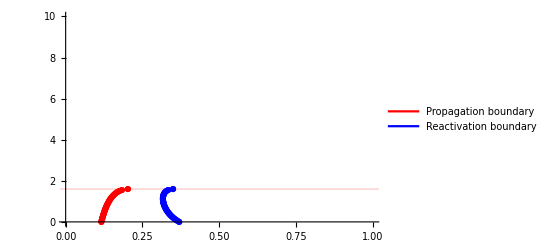

```mathematica
data=Transpose@{t1s,KlsEff};
data2=Transpose@{pares,KlsEff};
fig1=ListPlot[{data,data2},AxesLabel->{Style[MaTeX["\\tau[\\mu/k]",FontSize->30],Bold,16],Style[MaTeX["K_L[k/\\mu]",FontSize->30],Bold,16]},PlotRange->{{0,1},{0,10}}, PlotStyle->{Red,Blue},Joined->True,Mesh->Full,ImageSize->400,GridLines->{{},{{KlsEff[[Length[KlsEff]]],Red}}},PlotLegends->LineLegend[{"Propagation boundary","Reactivation boundary"},LegendMarkers->Automatic]]
```

```mathematica
Result for large middle-junction: T1=0.1, T2=0.2:
```

```mathematica
t1s = {};KlsEff ={};
Kls =Flatten[{{0},Range[150] 0.05}];
alpha=1;Ec=0.1;
For[i=1,i<Length[Kls]+1, i++,
Kl=Kls[[i]];
soln=Solve[{fftosolve/.{α->alpha, Subscript[ϵ, c]->Ec}/.{Subscript[K, L]->Kl}/.{Subscript[T, 1]->0.1, Subscript[T, 2]->0.2}} == 0 &&y>0 &&y<1,y, Reals];
If[Length[soln]>0,
tau=- Log[soln[[Length[soln],1,2]]];
AppendTo[t1s,tau];AppendTo[KlsEff,Kl]]];
pares={};
For[i=1,i<Length[KlsEff]+1, i++,
Kl=Kls[[i]];t1=t1s[[i]];
ss=Solve[FullSimplify[{qq/.{α->alpha, Subscript[ϵ, c]->Ec}/.{Subscript[K, L]->Kl}/.{Subscript[ta, 1]->t1}/.{Subscript[T, 1]->0.1, Subscript[T, 2]->0.2}}]==0&&τ≥t1 ,τ, Reals];
tt=ss[[Length[ss],1,2]];
AppendTo[pares,tt]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partd: Part specification {}⟦0,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

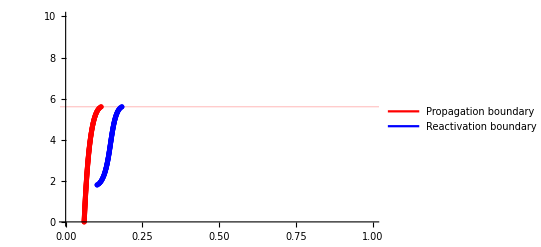

```mathematica
data=Transpose@{t1s,KlsEff};
data2=Transpose@{pares,KlsEff};
fig1=ListPlot[{data,data2},AxesLabel->{Style[MaTeX["\\tau[\\mu/k]",FontSize->30],Bold,16],Style[MaTeX["K_L[k/\\mu]",FontSize->30],Bold,16]},PlotRange->{{0,1},{0,10}}, PlotStyle->{Red,Blue},Joined->True,Mesh->Full,ImageSize->400,GridLines->{{},{{KlsEff[[Length[KlsEff]]],Red}}},PlotLegends->LineLegend[{"Propagation boundary","Reactivation boundary"},LegendMarkers->Automatic]]
```